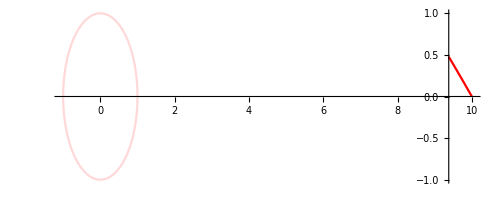

NDSolve::mxst: Maximum number of 1000 steps reached at the point τ == 32.0849.

```mathematica
(*M=10^12*)
(*G=6.67408*10^-11;
ε0=8.85418782×10-12;*)
ε=1;
rs= 1;
l=Sqrt[16]/2*rs;
t1=  2.3894;
t2=100;
t3=t1+(t2-t1)*2;
r0=10*rs;

RNt1= 60;
RNwt0= 32.08;
rq=0.95*rs/2;
RNrp=((rs/2)+Sqrt[(rs/2)^2-rq^2]);
RNrn=((rs/2)-Sqrt[(rs/2)^2-rq^2]);

transform=CoordinateTransformData["Polar"->"Cartesian","Mapping"];

s1=First@NDSolve[{D[r[τ],τ]==-Sqrt[(ε^2)-(1-(rs/r[τ]))(1+l^2/r[τ]^2)],r[0]==r0},r,{τ,0,t1},MaxSteps->1000];
ϕ1[τ_]:=NIntegrate[l/(r[t]/.s1)^2,{t,0,τ}];
plot1=ParametricPlot[transform[Evaluate[{r[τ]/.s1,ϕ1[τ]}]],{τ,0,t1},PlotStyle->Red];

(*s2=First@NDSolve[{D[r[τ],τ]==Sqrt[(ε^2)-(1-(rs/r[τ]))(1+l^2/r[τ]^2)],r[t1]==Re[r[t1]/.s1]+Re[r[t1]/.s1]/10000},r,{τ,t1,t2},MaxSteps->1000];
ϕ2[τ_]:=NIntegrate[l/(r[t]/.s2)^2,{t,0,τ}];
plot2=ParametricPlot[transform[Evaluate[{r[τ]/.s2,ϕ1[t1]+ϕ2[τ]}]],{τ,t1,t2},PlotStyle->Red];*)

scr=ParametricPlot[{rs*Cos[τ],rs*Sin[τ]},{τ,0,2*Pi},PlotStyle->LightRed];

fplot=Show[plot1,scr,PlotRange->All]
(*fplot=Show[plot1,plot2,scr,PlotRange->All]*)

RNs=First@NDSolve[{D[r[τ],τ]==-Sqrt[(ε^2)-(1-(rs/r[τ])+(rq^2/r[τ]^2))(1+l^2/r[τ]^2)],r[0]==r0},r,{τ,0,RNt1},MaxSteps->1000];
RNws=First@NDSolve[{D[r[τ],τ]==Sqrt[(ε^2)-(1-(rs/r[τ])+(rq^2/r[τ]^2))(1+l^2/r[τ]^2)],r[RNwt0]==Re[r[RNwt0]/.RNs]+Re[r[RNwt0]/.RNs]/10000},r,{τ,RNwt0,RNt1},MaxSteps->1000];

RNϕ[τ_]:=NIntegrate[l/(r[t]/.RNs)^2,{t,0,τ}];
RNwϕ[τ_]:=NIntegrate[l/(r[t]/.RNws)^2,{t,0,τ}];

RNplot=ParametricPlot[transform[Evaluate[{r[τ]/.RNs,RNϕ[τ]}]],{τ,0,RNt1},PlotStyle->Blue];
RNwplot=ParametricPlot[transform[Evaluate[{r[τ]/.RNws,RNϕ[RNwt0]+RNwϕ[τ]}]],{τ,RNwt0,RNt1},PlotStyle->Blue];
RNrpPlot=ParametricPlot[{RNrp*Cos[τ],RNrp*Sin[τ]},{τ,0,2*Pi},PlotStyle->LightBlue];
RNrnPlot=ParametricPlot[{RNrn*Cos[τ],RNrn*Sin[τ]},{τ,0,2*Pi},PlotStyle->LightBlue];

fplot=Show[RNplot,RNwplot,RNrpPlot,RNrnPlot,PlotRange->All]
(*fplot=Show[RNplot,RNrpPlot,RNrnPlot,PlotRange->All]*)

(*Plot[l^2/(r[τ]/.s)^2-rs/(r[τ]/.s)-(rs*l^2)/(r[τ]/.s)^3,{τ,0,t1},PlotRange->All]*)
(*Plot[r[τ]/.s,{τ,0,t1}]
Plot[ϕ[τ],{τ,0,t1}]*)
(*Plot[r[τ]/.qs,{τ,0,t1q}]
Plot[qϕ[τ],{τ,0,t1q}]*)


ep[r_]:=If[r<rs,1,-1];

(*U=2*rs*ep[r[t]/.s1]*Sqrt[Abs[((r[t]/.s1)/rs)-1]]Exp[-(t-(r[t]/.s1))/(2*rs)];
V=2*rs*Sqrt[Abs[((r[t]/.s1)/rs)-1]]Exp[(t+(r[t]/.s1))/(2*rs)];

pplot=ParametricPlot[{ArcTan[V/(2rs)],ArcTan[U/(2rs)]},{t,0,t1},PlotRange->{-Pi/2,Pi/2},PlotStyle->Red];
ppplot=ParametricPlot[{V,U},{t,0,t1},PlotStyle->Red];
pvesingplot=Plot[(Pi/2-x),{x,0,Pi/2}];
nvesingplot=Plot[(-Pi/2-x),{x,-Pi/2,0}];
rUV=rs(1+ProductLog[-(U*V)/(4 ⅇ rs^2)]);
Show[pplot,pvesingplot,nvesingplot]*)

ep[r_]:=If[r<rs,1,-1];
rt=(r[t]/.s1)+rs*Log[Abs[(r[t]/.s1)/rs-1]];
u=t-rt;
v=t+rt;
ep[r_]:=If[r<rs,1,-1];
U=2*rs*ep[r[t]/.s1]*Exp[-u/(2*rs)];
V=2*rs*1*Exp[v/(2*rs)];
pplot=ParametricPlot[{ArcTan[V/(2rs)],ArcTan[U/(2rs)]},{t,0,t1},PlotRange->{-Pi/2,Pi/2},PlotStyle->Red];
pvesingplot=Plot[(Pi/2-x),{x,0,Pi/2}];
nvesingplot=Plot[(-Pi/2-x),{x,-Pi/2,0}];


Show[pplot,pvesingplot,nvesingplot]




(*ap=RNrp^2/(RNrp-RNrn);
an=RNrn^2/(RNrn-RNrp);

lam=(2*an)^-1;

RNU=ep[(r[t]/.RNs)]/lam * Abs[(r[t]/.RNs)/RNrp-1]^(lam*ap)* Abs[(r[t]/.RNs)/RNrn-1]^(lam*an)Exp[-lam*(t-(r[t]/.RNs))];
RNV=1/lam * Abs[(r[t]/.RNs)/RNrp-1]^(lam*ap)* Abs[(r[t]/.RNs)/RNrn-1]^(lam*an)Exp[lam*(t+(r[t]/.RNs))];

pplot=ParametricPlot[{ArcTan[RNV/(2*an)],ArcTan[RNU/(2*an)]},{t,0,RNt1},PlotRange->{-Pi/2,Pi/2},PlotStyle->Red];
pvesingplot=Plot[(Pi/2-x),{x,0,Pi/2}];
nvesingplot=Plot[(-Pi/2-x),{x,-Pi/2,0}];

Show[pplot,pvesingplot,nvesingplot]*)
```

```mathematica
(*
Export["C:\Users\mogzy\OneDrive - Swansea University\Dis\Task 4.2 plots\ε="<>ToString[ε]<>", rs="<>ToString[rs]<>", l="<>ToString[l]<>", r0="<>ToString[r0]<>", rq="<>ToString[rq]<>".png",fplot]*)
```

10

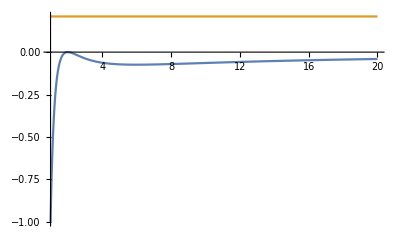

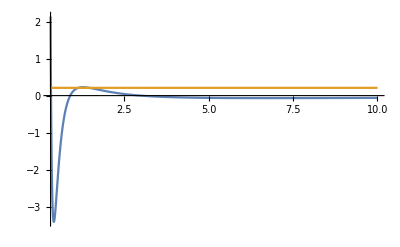

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{r→0.417561},{r→1.28013},{r→6.75356}}

```mathematica
ε=1.1;
rs= 1;
r0=10*rs
l=Sqrt[16]/2*rs;
rq=0.95*rs/2;

Plot[{l^2/(rr)^2-rs/(rr)-(rs*l^2)/(rr)^3,ε^2-1},{rr,rs/1,r0*2},PlotRange->All]
Plot[{(1-rs/r+rq^2/r^2)(l^2/r^2+1)-1,ε^2-1},{r,0.32,r0},PlotRange->All]
re=Solve[D[(1-rs/r+rq^2/r^2)(l^2/r^2+1)-1,r]==0,r]
e[re_]:=(1-rs/(re)+rq^2/(re)^2)(l^2/(re)^2+1)-1
```

```mathematica
e[1.2801321863196842]
```

```mathematica
0.22672564991424138
```

```mathematica
Sqrt[e[1.2801321863196842]+1]
```

```mathematica
0758
```

```mathematica
Solve[UU*VV==4*rss^2(1-rrr/rss)Exp[rrr/rss],rrr]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{rrr→rss (1+ProductLog[-(UU VV)/(4 ⅇ rss^2)])}}

```mathematica
First[{{rrr->rss (1+ProductLog[-(UU VV)/(4 ⅇ rss^2)])}}]
```

{rrr→rss (1+ProductLog[-(UU VV)/(4 ⅇ rss^2)])}

```mathematica
{rrr->rss (1+ProductLog[-(UU VV)/(4 ⅇ rss^2)])}/.Rule->Equal
```

{rrr==rss (1+ProductLog[-(UU VV)/(4 ⅇ rss^2)])}